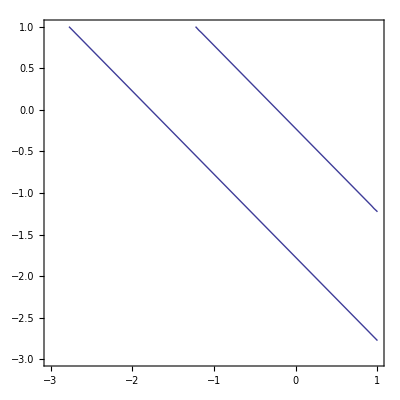

```mathematica
A={{1,1},{1,1}};b={2,2};c=0.4;
f[x_]:=x.A.x+b.x+c;
ContourPlot[f[{x1,x2}]==0,{x1,-3,1},{x2,-3,1}]
```

```mathematica
Clear[A,b,c]
A[a_]:={{1,0},{0,a}};
b = {2,2};
f[x_,a_,c_]:=x.A[a].x+b.x+c;
Animate[ContourPlot[f[{x1,x2},a,-1]==0,{x1,-5,5},{x2,-5,5},PlotPoints->25],{a,-1,1}]
```

```mathematica
Clear[A,a,x1,x2];
A[a_]:={{a,0},{0,0}};
Animate[ContourPlot[x1^2+a*x2-1==0,{x1,-10,10},{x2,-10,10},PlotPoints->25],{a,-1,1}]
```

```mathematica
A=DiagonalMatrix[{1,1,1}];
b = {2,1,3};
c=-1;
f[x_]:=x.A.x+b.x + c;
ContourPlot3D[f[{x1,x2,x3}]==0,{x1,-2,2},{x2,-2,2},{x3,-2,2}]
```

-Graphics3D-